# MATRIX STRUCTURE

## For the coupling matrices to the LH fields of the S_1 leptoquark introducing a FN symmetry.

## Initialization and constants

```mathematica
hbar=6.582119*10^-25; (*GeV*s*)
secPerYear=3600*24*365.25;
hbary=hbar/secPerYear;

(* CKM and PMNS matrices *)
V= {{0.97435,0.22501,0.00373},{0.22487,0.97349,0.04183},{0.00858,0.04111,0.99912}};
U={{0.82296,0.54843,0.14815},{0.27528,0.61286,0.74069},{0.49695,0.56888,0.65531}};

(* 3rd generation charges *)
Qq3=0;
Ql3=0;

(* masses in GeV *)
mp=0.938272;
me=0.000511;
mmu=0.105658;
mpi0=0.134977;
mpiPlus=0.139570;
mK=0.493677;
meta = 0.54786;
mrho0=0.77503;
mrhoPlus=0.77511;
momega=0.78266;
mK0=0.49761;
mLQ=10000; (*10 TeV*)
Lambda= 10^16; (*GeV*) (* GUT scale *)

(* Renormalization group factor *)
AL = 1.4;
(* Lattice QCD form factor *)
W0benchmark=0.1;
W0EpiL= 0.134;
W0EpiR=-0.131;
W0MupiL=0.119;
W0MupiR=-0.118;
W0NupiL=0.189;
W0NupiR=-0.186;
W0NuKR=-0.134;
W0NuKL=0.139;
W0EetaR=0.006;
W0EetaL=0.113;
W0MuetaR=0.011;
W0MuetaL=0.108;


(* CM momentums: p=(1/(2mp))*Sqrt[(mp^2-mf1^2-mf2^2)^2-4*mf1^2*mf2^2] *)
pepi0=(1/(2*mp))*Sqrt[(mp^2-me^2-mpi0^2)^2-4*me^2*mpi0^2];
pmupi0=(1/(2*mp))*Sqrt[(mp^2-mmu^2-mpi0^2)^2-4*mmu^2*mpi0^2];
pnupiPlus=(1/(2*mp))*(mp^2-mpiPlus^2);
pnuK=(1/(2*mp))*(mp^2-mK^2);
peeta=(1/(2*mp))*Sqrt[(mp^2-me^2-meta^2)^2-4*me^2*meta^2];
pmueta=(1/(2*mp))*Sqrt[(mp^2-mmu^2-meta^2)^2-4*mmu^2*meta^2];
perho=(1/(2*mp))*Sqrt[(mp^2-me^2-mrho0^2)^2-4*me^2*mrho0^2];
pmurho=(1/(2*mp))*Sqrt[(mp^2-mmu^2-mrho0^2)^2-4*mmu^2*mrho0^2];
pnurho=(1/(2*mp))*(mp^2-mrhoPlus^2);
peomega=(1/(2*mp))*Sqrt[(mp^2-me^2-momega^2)^2-4*me^2*momega^2];
pmuomega=(1/(2*mp))*Sqrt[(mp^2-mmu^2-momega^2)^2-4*mmu^2*momega^2];
peK0=(1/(2*mp))*Sqrt[(mp^2-me^2-mK0^2)^2-4*me^2*mK0^2];
pmuK0=(1/(2*mp))*Sqrt[(mp^2-mmu^2-mK0^2)^2-4*mmu^2*mK0^2];

(* K prefactors assuming the leptoquark mass is inside this because we are taking it as a constant *)
KEpi0 = pepi0/(16*Pi*mp^2)*(AL^2 * W0EpiL^2)/mLQ^4*(mp^2+me^2-mpi0^2);
KMupi0= pmupi0/(16*Pi*mp^2)*(AL^2 * W0MupiL^2)/mLQ^4*(mp^2+mmu^2-mpi0^2);
KNupiPlus=pnupiPlus/(16*Pi*mp^2)*(AL^2 * W0NupiL^2)/mLQ^4*(mp^2-mpiPlus^2);
KNuK=pnuK/(16*Pi*mp^2)*(AL^2 * W0NuKL^2)/mLQ^4*(mp^2-mK^2);
KEeta=peeta/(16*Pi*mp^2)*(AL^2 * W0EetaL^2)/mLQ^4*(mp^2+me^2-meta^2);
KMueta=pmueta/(16*Pi*mp^2)*(AL^2 * W0MuetaL^2)/mLQ^4*(mp^2+mmu^2-meta^2);
KErho0= perho/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+me^2-mrho0^2);
KMurho0=pmurho/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+mmu^2-mrho0^2);
KNurhoPlus = pnurho/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2-mrhoPlus^2);
KEomega=peomega/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+me^2-momega^2);
KMuomega=pmuomega/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+mmu^2-momega^2);
```

```mathematica
(* PDG experimental bounds (in years)*)
limEpi=2.4*10^34;
limMupi=1.6*10^34;
limNuPi=3.9*10^32;
limNuK=5.9*10^34;
limEeta=1.0*10^34;
limMueta=4.7*10^33;
limErho=7.2*10^32;
limMurho=5.7*10^32;
limNurho=1.62*10^32;
limEomega=1.6*10^33;
limMuomega=2.8*10^33;
```

## Monte Carlo scan

### Core

```mathematica
(*This function searches in the parameter space for variables that fit the PDG limits*)ScanProtonDecay[nLimits_,numSamples_,maxCharge_]:=Module[{results={},safetyFactors, minRobustness, bottleneckIdx, channelNames,bottleneck},
channelNames={"p->e^+π^0","p->μ^+π^0","p-> ν̄ π^+","p-> ν̄ K^+"};
Do[(*Assign random values to the exponents*)
{Qq1,Qq2,Ql1,Ql2}=RandomInteger[{-maxCharge,maxCharge},4];
eps=RandomReal[{10^-3,0.25}];

(*Reconstruct the coupling matrices*)y1LL={{eps^Abs[Qq1+Ql1],eps^Abs[Qq1+Ql2],eps^Abs[Qq1+Ql3]},{eps^Abs[Qq2+Ql1],eps^Abs[Qq2+Ql2],eps^Abs[Qq2+Ql3]},{eps^Abs[Qq3+Ql1],eps^Abs[Qq3+Ql2],1}};
z1LL={{eps^Abs[2*Qq1],eps^Abs[Qq1+Qq2],eps^Abs[Qq1+Qq3]},{eps^Abs[Qq1+Qq2],eps^Abs[2*Qq2],eps^Abs[Qq2+Qq3]},{eps^Abs[Qq1+Qq3],eps^Abs[Qq2+Qq3],1}};
(*Effective matrices*)
yEff=V.y1LL;
zEff=V.z1LL;
hEff=y1LL.U;

(*Recalculate lifetimes*)
tauEpi0=hbary/(KEpi0*Abs[zEff[[1,1]]*yEff[[1,1]]]^2);
tauMupi=hbary/(KMupi0*Abs[zEff[[1,1]]*yEff[[1,2]]]^2);
tauNuPi=hbary/(KNupiPlus*Abs[zEff[[1,1]]*(hEff[[1,1]]+hEff[[1,2]]+hEff[[1,3]])]^2);
tauNuK=hbary/(KNuK*Abs[zEff[[1,1]]*(hEff[[2,1]]+hEff[[2,2]]+hEff[[2,3]])]^2);
(*VEV calculation*)
Vev=eps*Lambda;(*GeV*)

(*Acumulative filter for each number of limits fulfilled*)isOk=Which[nLimits==1,tauEpi0>limEpi,nLimits==2,tauEpi0>limEpi&&tauMupi>limMupi,nLimits==3,tauEpi0>limEpi&&tauMupi>limMupi&&tauNuPi>limNuPi,nLimits==4,tauEpi0>limEpi&&tauMupi>limMupi&&tauNuPi>limNuPi&&tauNuK>limNuK];
If[isOk,
safetyFactors={tauEpi0/limEpi,tauMupi/limMupi,tauNuPi/limNuPi,tauNuK/limNuK};
minRobustness=Min[safetyFactors];
bottleneckIdx=Ordering[safetyFactors,1][[1]];
bottleneck=channelNames[[bottleneckIdx]];
AppendTo[results,{eps,Qq1,Qq2,Qq3,Ql1,Ql2,Ql3,Vev,minRobustness,bottleneck}]],{numSamples}];
Return[results]];
```

### maxCharge evaluation

General::munfl: 6.24846×10^-20 3.56853×10^-296 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.84835×10^-20 2.26435×10^-301 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.50155×10^-161)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

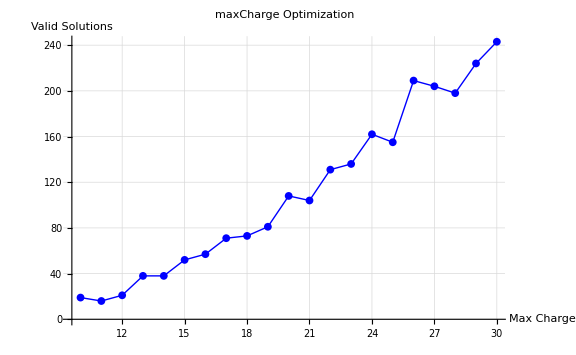

monte_carlo_optimization.png

```mathematica
chargeThresholdTest=Table[{mCharge,Length[ScanProtonDecay[4,1000,mCharge]]},{mCharge,10,30}];

ListLinePlot[chargeThresholdTest,PlotMarkers->{Automatic,8},PlotLabel->Style["maxCharge Optimization",18,Bold,Black],AxesLabel->{Style["Max Charge",15,Bold,Black],Style["Valid Solutions",15,Bold,Black]},PlotStyle->{Directive[Blue,Thick]},AxesStyle->Directive[Black,Thick],GridLines->Automatic,GridLinesStyle->Directive[Black,Dotted,Opacity[0.4]],BaseStyle->{FontSize->14,FontFamily->"Helvetica",FontWeight->Bold},ImageSize->Large,PlotRange->All]
```

### Ejecution

```mathematica
(*Ejecution for x limits and y iterations and z maxCharge*)
mysolutions=ScanProtonDecay[4,1000000,23];

Print["Number of solutions found: ",Length[mysolutions]];
sortedSolutions=SortBy[mysolutions,#[[9]] &];

If[Length[mysolutions]>0,TableForm[Take[sortedSolutions,Min[Length[sortedSolutions],10]],TableHeadings->{None,{"eps","Qq1","Qq2","Qq3","Ql1","Ql2","Ql3","vev","robustness factor","less robust channel"}}]]
```

Number of solutions found: 141080

eps | Qq1 | Qq2 | Qq3 | Ql1 | Ql2 | Ql3 | vev | robustness factor | less robust channel
0.125889 | -21 | -10 | 0 | -13 | 23 | 0 | 1.25889×10^15 | 1.00007 | p->μ^+π^0
0.00924396 | -5 | -18 | 0 | -16 | -9 | 0 | 9.24396×10^13 | 1.0005 | p-> ν̄ π^+
0.12573 | 18 | 17 | 0 | 6 | -23 | 0 | 1.2573×10^15 | 1.00069 | p->μ^+π^0
0.00125543 | 20 | -14 | 0 | 16 | 12 | 0 | 1.25543×10^13 | 1.00083 | p-> ν̄ K^+
0.106667 | -14 | -13 | 0 | 5 | -18 | 0 | 1.06667×10^15 | 1.00088 | p->e^+π^0
0.0905593 | -22 | 2 | 0 | 12 | 18 | 0 | 9.05593×10^14 | 1.00096 | p-> ν̄ K^+
0.0188344 | 7 | 23 | 0 | 19 | -12 | 0 | 1.88344×10^14 | 1.00127 | p->μ^+π^0
0.195618 | 19 | 12 | 0 | 7 | 23 | 0 | 1.95618×10^15 | 1.00133 | p->e^+π^0
0.134695 | 20 | 21 | 0 | 11 | 1 | 0 | 1.34695×10^15 | 1.00145 | p->μ^+π^0
0.0863195 | 20 | 2 | 0 | -2 | -17 | 0 | 8.63195×10^14 | 1.0016 | p-> ν̄ K^+

### Epsilon histogram

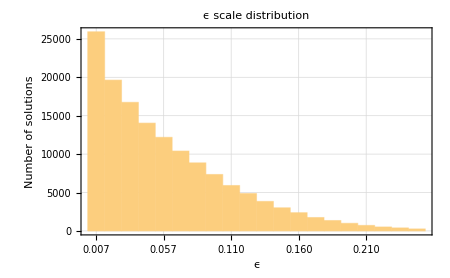

eps_distribution_LHFN.png

```mathematica
epsData=mysolutions[[All,1]];
minVal=Min[epsData];
maxVal=Max[epsData];
numBins=20;

(* binning *)
binEdges=Subdivide[minVal,maxVal,numBins];
binCenters=Table[(binEdges[[i]]+binEdges[[i+1]])/2,{i,1,Length[binEdges]-1}];
step=4;
customTicks=Table[{binCenters[[i]],NumberForm[binCenters[[i]],{2,3}]},{i,1,Length[binCenters],step}];

(*histogram*)
myPlot=Histogram[epsData,{minVal,maxVal,(maxVal-minVal)/numBins},PlotLabel->Style["ϵ scale distribution",18,Bold,Black],Frame->{{True,False},{True,False}},FrameLabel->{Style["ϵ",18,Bold,Black],Style["Number of solutions",16,Bold,Black]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dotted,Opacity[0.4]],FrameStyle->Directive[Black,Thick],FrameTicks->{{Automatic,None},{customTicks,None}},BaseStyle->{FontSize->14,FontFamily->"Helvetica",Black},LabelStyle->{FontSize->14,Bold,Black},ImagePadding->{{75,15},{45,10}},ImageSize->450]
Export["eps_distribution_LHFN.png",myPlot]
```

### Charge distribution

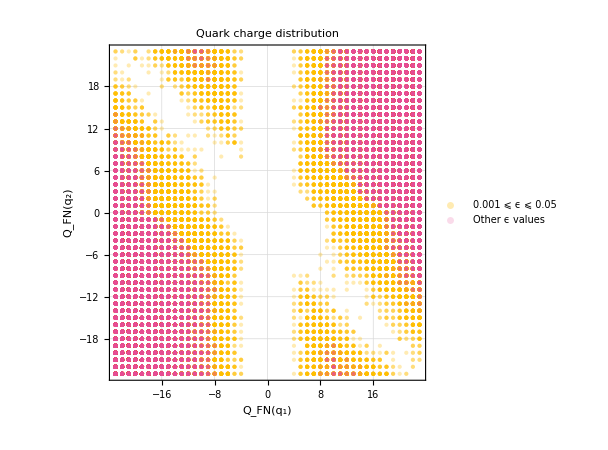

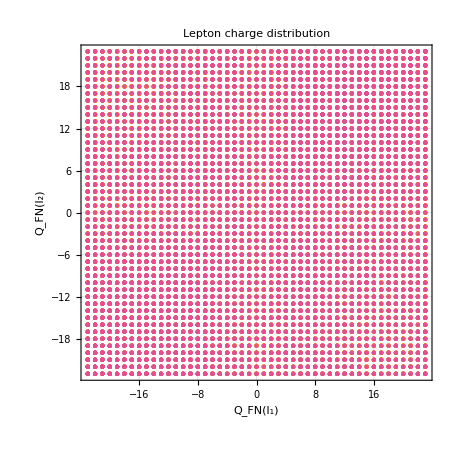

```mathematica
(* Separate data based on the epsilon value *)
yellowData=Select[mysolutions,0.001<=#[[1]]<=0.05&];
pinkData=Select[mysolutions,#[[1]]<0.001||#[[1]]>0.05&];

(* quark charge distribution *)
plotQq=ListPlot[{yellowData[[All,{2,3}]],pinkData[[All,{2,3}]]},PlotStyle->{Directive[RGBColor[1,0.75,0],Opacity[0.3],PointSize[Medium]],(*Translucent yellow/amber*)Directive[RGBColor[0.9,0.3,0.6],Opacity[0.2],PointSize[Medium]]  (*Lower opacity pink*)},
PlotRange->{{-23,23},{-23,23}},AspectRatio->1.0,Frame->True,FrameStyle->Directive[Gray,Thick],Axes->True,AxesOrigin->{0,0},AxesStyle->Directive[Black,Thick],FrameLabel->{Style[Subscript[Q,"FN"][Subscript[q,1]],18,Bold,Black],Style[Subscript[Q,"FN"][Subscript[q,2]],18,Bold,Black]},PlotLabel->Style["Quark charge distribution",18,Bold,GrayLevel[0.3]],GridLines->Automatic,GridLinesStyle->Directive[LightGray,Opacity[0.7]],PlotLegends->{"0.001 ⩽ ϵ ⩽ 0.05","Other ϵ values"},BaseStyle->{FontSize->14,FontFamily->"Helvetica",Black},ImageSize->450]

(* lepton charge distribution *)
plotQl=ListPlot[{yellowData[[All,{5,6}]],pinkData[[All,{5,6}]]},PlotStyle->{Directive[RGBColor[1,0.75,0],Opacity[0.3],PointSize[Medium]],Directive[RGBColor[0.9,0.3,0.6],Opacity[0.2],PointSize[Medium]]},PlotRange->{{-23,23},{-23,23}},AspectRatio->1.0,Frame->True,FrameStyle->Directive[Gray,Thick],Axes->True,AxesOrigin->{0,0},AxesStyle->Directive[Black,Thick],FrameLabel->{Style[Subscript[Q,"FN"][Subscript[l,1]],18,Bold,Black],Style[Subscript[Q,"FN"][Subscript[l,2]],18,Bold,Black]},PlotLabel->Style["Lepton charge distribution",18,Bold,GrayLevel[0.3]],GridLines->Automatic,GridLinesStyle->Directive[LightGray,Opacity[0.7]],BaseStyle->{FontSize->14,FontFamily->"Helvetica",Black},ImageSize->450]

(*Export both plots in high resolution (PNG at 300 DPI)*)
Export["dist_qcharges_LHFN.png",plotQq,ImageResolution->300];
Export["dist_lcharges_LHFN.png",plotQl,ImageResolution->300];
```

## Grid search

```mathematica
eps=0.001;
maxCharge=23;
channelNames={"p->e^+π^0","p->μ^+π^0","p-> ν̄ π^+","p-> ν̄ K^+"};

totalIterations=0; 

(*Systematic grid search*)
gridResults=Reap[Do[totalIterations++;(*Reconstruct the coupling matrices*)y1LL={{eps^Abs[q1+l1],eps^Abs[q1+l2],eps^Abs[q1+Ql3]},{eps^Abs[q2+l1],eps^Abs[q2+l2],eps^Abs[q2+Ql3]},{eps^Abs[Qq3+l1],eps^Abs[Qq3+l2],1}};
z1LL={{eps^Abs[2*q1],eps^Abs[q1+q2],eps^Abs[q1+Qq3]},{eps^Abs[q1+q2],eps^Abs[2*q2],eps^Abs[q2+Qq3]},{eps^Abs[q1+Qq3],eps^Abs[q2+Qq3],1}};
(*Effective matrices and lifetime calculations*)
yEff=V.y1LL;
zEff=V.z1LL;
hEff=y1LL.U;

tauEpi0=hbary/(KEpi0*Abs[zEff[[1,1]]*yEff[[1,1]]]^2);
tauMupi=hbary/(KMupi0*Abs[zEff[[1,1]]*yEff[[1,2]]]^2);
tauNuPi=hbary/(KNupiPlus*Abs[zEff[[1,1]]*(hEff[[1,1]]+hEff[[1,2]]+hEff[[1,3]])]^2);
tauNuK=hbary/(KNuK*Abs[zEff[[1,1]]*(hEff[[2,1]]+hEff[[2,2]]+hEff[[2,3]])]^2);

(*Check PDG bounds*)
isOk=(tauEpi0>limEpi)&&(tauMupi>limMupi)&&(tauNuPi>limNuPi)&&(tauNuK>limNuK);
If[isOk,safetyFactors={tauEpi0/limEpi,tauMupi/limMupi,tauNuPi/limNuPi,tauNuK/limNuK};
minRobustness=Min[safetyFactors];
bottleneckIdx=Ordering[safetyFactors,1][[1]];
criticalChannel=channelNames[[bottleneckIdx]];
Sow[{q1,q2,l1,l2,minRobustness,criticalChannel}]],{q1,-maxCharge,maxCharge},{q2,0,maxCharge},{l1,-maxCharge,maxCharge},{l2,-maxCharge,maxCharge}]];

(*Extract solutions and sort by robustness factor (tightest first)*)
allGridSolutions=If[Length[gridResults[[2]]]>0,gridResults[[2,1]],{}];
sortedGridSolutions=SortBy[allGridSolutions,#[[5]]&];

Print["Number of solutions found: ", Length[sortedGridSolutions], " → ", N[Length[sortedGridSolutions]/(totalIterations) *100], " % of the parameter space"]

(*Display the lowest R solutions in table format*)
If[Length[sortedGridSolutions]>0,TableForm[Take[sortedGridSolutions,Min[Length[sortedGridSolutions],20]],TableHeadings->{None,{"Q(q1)","Q(q2)","Q(l1)","Q(l2)","robustness factor","critical channel"}}],Print["No solutions found in this range."]]
```

Number of solutions found: 1631213 → 65.4645 % of the parameter space

Q(q1) | Q(q2) | Q(l1) | Q(l2) | robustness factor | critical channel
-5 | 11 | 3 | -23 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -22 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -21 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -20 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -19 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -18 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -17 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -16 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -15 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -14 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -8 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -7 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -6 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -5 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -4 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -3 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | -2 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | 2 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | 3 | 1.85777 | p->e^+π^0
-5 | 11 | 3 | 7 | 1.85777 | p->e^+π^0

## Visualization: interactive sliders

```mathematica
(*--- MANIPULATE ---*)
Manipulate[
(*Matrices Definition*)
y1LL={{eps^Abs[Qq1+Ql1],eps^Abs[Qq1+Ql2],eps^Abs[Qq1+Ql3]},
{eps^Abs[Qq2+Ql1],eps^Abs[Qq2+Ql2],eps^Abs[Qq2+Ql3]},
{eps^Abs[Qq3+Ql1],eps^Abs[Qq3+Ql2],1}};
z1LL={{eps^Abs[2*Qq1],eps^Abs[Qq1+Qq2],eps^Abs[Qq1+Qq3]},
{eps^Abs[Qq1+Qq2],eps^Abs[2*Qq2],eps^Abs[Qq2+Qq3]},
{eps^Abs[Qq1+Qq3],eps^Abs[Qq2+Qq3],1}};

(*Effective Matrices*)
yEff=V.y1LL;
zEff=V.z1LL;
hEff=y1LL.U;

(*Lifetime Calculations*)
tauEpi0=hbary/(KEpi0*Abs[zEff[[1,1]]*yEff[[1,1]]]^2);
tauMupi=hbary/(KMupi0*Abs[zEff[[1,1]]*yEff[[1,2]]]^2);
tauNuPi=hbary/(KNupiPlus*Abs[zEff[[1,1]]*(hEff[[1,1]]+hEff[[1,2]]+hEff[[1,3]])]^2);
tauNuK=hbary/(KNuK*Abs[zEff[[1,1]]*(hEff[[2,1]]+hEff[[2,2]]+hEff[[2,3]])]^2);
tauEeta=tauEpi0*KEpi0/KEeta;
tauMueta=tauMupi*KMupi0/KMueta;
tauErho=tauEpi0*KEpi0/KErho0;
tauMurho=tauMupi*KMupi0/KMurho0;
tauNurhoPlus=tauNuPi*KNupiPlus/KNurhoPlus;
tauEomega=tauEpi0*KEpi0/KEomega;
tauMuomega=tauMupi*KMupi0/KMuomega;

(*Visualization*)Column[{Style["Coupling Matrices (Flavor Basis)",Bold,16],Row[{Style["y1LL = ",14],MatrixForm[y1LL],Spacer[30],Style["z1LL = ",14],MatrixForm[z1LL]}],Spacer[20],Grid[{{Style["Results: Proton lifetime (years)",Bold,16]},{Grid[{{Style["Channel",Bold],Style["Theoretical Tau [years]",Bold],Style["PDG bound [years]",Bold],Style["Status",Bold]},{"p → e^+ π^0",ScientificForm[tauEpi0,3],ScientificForm[limEpi,3],If[tauEpi0>limEpi,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → μ^+ π^0",ScientificForm[tauMupi,3],ScientificForm[limMupi,3],If[tauMupi>limMupi,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → ν̄ π^+",ScientificForm[tauNuPi,3],ScientificForm[limNuPi,3],If[tauNuPi>limNuPi,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → ν̄ K^+",ScientificForm[tauNuK,3],ScientificForm[limNuK,3],If[tauNuK>limNuK,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → e^+ η",ScientificForm[tauEeta,3],ScientificForm[limEeta,3],If[tauEeta>limEeta,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → μ^+ η",ScientificForm[tauMueta,3],ScientificForm[limMueta,3],If[tauMueta>limMueta,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → e^+ ρ^0",ScientificForm[tauErho,3],ScientificForm[limErho,3],If[tauErho>limErho,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → μ^+ ρ^0",ScientificForm[tauMurho,3],ScientificForm[limMurho,3],If[tauMurho>limMurho,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → ν̄ ρ^+",ScientificForm[tauNurhoPlus,3],ScientificForm[limNurho,3],If[tauNurhoPlus>limNurho,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → e^+ ω",ScientificForm[tauEomega,3],ScientificForm[limEomega,3],If[tauEomega>limEomega,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → μ^+ ω",ScientificForm[tauMuomega,3],ScientificForm[limMuomega,3],If[tauMuomega>limMuomega,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]}},
Frame->All,Background->{None,{LightGray,White}},Alignment->Left]}}]}],

(*Explicit Controls*)
Delimiter,
Style["Global Parameters",Bold],{{eps,0.001,"ϵ"},0.001,0.25,Appearance->"Labeled"},
Style["Exponents y1LL",Bold],
{{Qq1,-5,"Qq1"},-20,20,1,Appearance->"Labeled"},
{{Qq2,11,"Qq2"},-20,20,1,Appearance->"Labeled"},
{{Ql1,3,"Ql1"},-20,20,1,Appearance->"Labeled"},
{{Ql2,2,"Ql2"},-20,20,1,Appearance->"Labeled"},
ControlPlacement->Left,TrackedSymbols:>All]
```